# ME314 - Final Project Gerik Zatorski

```mathematica
Quit[];
```

## Phase 1 (hold -> roll)

```mathematica
(* Initialization Stuff *)

ClearAll["Global`*"]

θBall[t_]=Piecewise[{
{θBallBefore,0<t<tRoll},
{θBallRolling,tRoll<t<tRelease},
{θBallSimulate,tRelease<t}
}];

(* SE(2) representation of rigid body motion in the plane *)
g[x_,y_,θ_]={{Cos[θ],-Sin[θ],x},{Sin[θ],Cos[θ],y},{0,0,1}};
(* unhat takes a 3x3 matrix that is assumed to be ginv.gdot for SE(2) and returns a 3x1 vector. The first two components are the linear velocities in x and y and the third component is the angular velocity (around the "z" axis that is out of the plane of motion *)
unhat[a_]:={a[[1,3]],a[[2,3]],a[[2,1]]};
(* hat[] takes a 3x1 vector and creates a 3x3 matrix *)
hat[a_]:={{0,-a[[3]],a[[1]]},{a[[3]],0,a[[2]]},{0,0,0}};
(* Hom[] takes a point in the plane and adds a 1 to the end of it to create a homogeneous representation of that point. This is used for animation *)
Hom[pt_]:=Flatten[{pt,1}];
(* UnHom[] takes a homogeneous representation of a point and returns the point in the plane by removing the 1 at the end *)
UnHom[pt_]:={pt[[1]],pt[[2]]};
(* Distance between two points in 2D plane *)
Distance2D[x_,y_]:=Sqrt[(x[[1]]-y[[1]])^2+(x[[2]]-y[[2]])^2];

(* Conversions *)
FtToM=0.3048;

(* Ball Constants *)
m=0.625;
diameterBall=9.55/12*FtToM;
rBall=diameterBall/2;

(* link dimensions *)
L1=.4;

(* Joint Frame Transformations *)
g0=g[0,0,θ0[t]];
ghand=g0.g[L1/2,0,0];
g2=g0.g[L1,0,θ2[t]];

(* Ball Frame Transformations *)
gBallHold=g0.g[L1/2,rBall,0]; (* transformation before ball is released from constraint *)
gline1Hold=gBallHold.g[-rBall,0,0];
gline2Hold=gBallHold.g[rBall,0,0];

(* Fake Joint Positions *)
tMax=5/4;
θ0sol=ListInterpolation[Pi/12*{-3,5},{0,tMax}][t];
(*θ0sol=ListInterpolation[Pi/12*{-1,-1},{0,tMax}][t]; (*static test*)*)
θBallBefore=θ0sol

(* Fake Joint Velocities and Accelerations *)
θ0dotsol = D[θ0sol,t];
θ0dotdotsol = D[θ0dotsol,t];

(* ################################################## *)
(* Coordinates and Graphics Primatives *)
(* ################################################## *)

(* Dynamic Joint Coordinates *)
coordj0[time_]:=({g0[[1,3]],g0[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;
coordj2[time_]:=({g2[[1,3]],g2[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time

(* Ball Coordinates *)
coordBallHold[time_]:=({gBallHold[[1,3]],gBallHold[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;
coordline1Hold[time_]:=({gline1Hold[[1,3]],gline1Hold[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;
coordline2Hold[time_]:=({gline2Hold[[1,3]],gline2Hold[[2,3]]}/.{θ0[t]->θ0sol,θ2[t]->θ2sol})/.t->time;

(* Dynamic Graphics Primatives *)
graphicL1=Line[{coordj0[t],coordj2[t]}];
graphicBallHold = Circle[coordBallHold[t],rBall];
graphicBallLineHold=Line[{coordline1Hold[t],coordline2Hold[t]}];

graphicBall=Circle[{xsol,ysol},diameterBall/2];


(* Environment Static Coordinates *)
coordLeftRim={-7,2};
coordRightRim={-6,2};
coordBackboardBottom={-7.2,1.8};
coordBackboardTop={-7.2,3.8};

(* Environment Static Graphics *)
graphicBackboard=Line[{coordBackboardBottom,coordBackboardTop}];
graphicLeftRim=Disk[coordLeftRim,RimThickness/2];
graphicRightRim=Disk[coordRightRim,RimThickness/2];


(* ################################################## *)
(* Solving for conditions at roll start *)
(* ################################################## *)

tRoll=0.05;
tr=gBallHold/.{θ0[t]->θ0sol};
xr=tr[[1,3]]/.t->tRoll;
yr=tr[[2,3]]/.t->tRoll;
θr=θ0[t]/.{θ0[t]->θ0sol}/.t->tRoll;

(* dot sol exact *)
θrdot=θ0dotsol/.t->tRoll;
trdot=D[gBallHold,t]/.{θ0[t]->θ0sol,θ0'[t]->θ0dotsol};
xrdot=trdot[[1,3]]/.t->tRoll;
yrdot=trdot[[2,3]]/.t->tRoll;

(* Plots *)
(*Plot[θ0sol,{t,0,tMax}]
Plot[θ0dotsol,{t,0,tMax}]*)

(* Animations *)
Animate[
Show[
Graphics[{
Black,graphicL1/.t->time,
Black,graphicBallHold/.t->time,
Black,graphicBallLineHold/.t->time
},Axes->True]
],
{time,0,tMax},
AnimationRunning->False,
AnimationRate->1.0
]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {1}.

5
InterpolatingFunction[{{0, -}}, <>]
                           4[t]

## Phase 2 (roll -> release)

```mathematica
(* New Ball Frame Transforms for time after roll *)
gball=g[x[t],y[t],θ[t]];
ghandball=Inverse[ghand].gball; (* ball in hand frame *)
θhandball=θ[t]-θ0[t];
xhandball=ghandball[[1,3]];
gcontact=g0.g[L1/2-rBall*θhandball,0,0];
 
(* Configuration Variables *)
q={{x[t],y[t],θ[t]}}ᵀ;
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian using body velocities (see lecture 23) *)
Vball=unhat[Inverse[gball].D[gball,t]];
Iball=DiagonalMatrix[{m,m,J}];
J=m*rBall^2;
KE=1/2*(Vball.Iball).{Vball}ᵀ;
PE=m*grav*y[t];
Lag =KE-PE;

(***************************************************************************)
(* Constraints and External forces *)
(***************************************************************************)

(* Point of contact *)
mhand=(g2[[2,3]]-g0[[2,3]])/(g2[[1,3]]-g0[[1,3]]);
Eqhand=contacty-g2[[2,3]]==mhand*(contactx-g2[[1,3]]);
Eqprojection=contacty-gball[[2,3]]==-1/mhand*(contactx-gball[[1,3]]);
contacttemp=Solve[{Eqhand&&Eqprojection},{contactx,contacty}];
contactx=contacttemp[[1,1,2]];
contacty=contacttemp[[1,2,2]];

(* Constraints *)
(* Ball remains in contact with last link *)
ϕa=ghandball[[2,3]]+rBall;

(* Ball rolls without slipping where x=rBall*θ *)
ϕb=xhandball+rBall*θhandball;

(* gotta do this *)
θ0[t]=θ0sol;
θ0'[t]=θ0dotsol;
θ0''[t]=θ0dotdotsol;

(***************************************************************************)
(* Euler-Lagrange equations VECTORS *)
(***************************************************************************)

(* Using BOTH Constraints *)
Eq1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]==λa*D[ϕa,x[t]]+λb*D[ϕb,x[t]];
Eq2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]==λa*D[ϕa,y[t]]+λb*D[ϕb,y[t]];
Eq3=D[D[Lag,θ'[t]],t]-D[Lag,θ[t]]==λa*D[ϕa,θ[t]]+λb*D[ϕb,θ[t]];
Eq4=D[D[ϕa,t],t]==0;
Eq5=D[D[ϕb,t],t]==0;
ELtemp=Solve[{Eq1&&Eq2&&Eq3&&Eq4&&Eq5},{x''[t],y''[t],θ''[t],λa,λb}];

EL={x''[t]==ELtemp[[1,1,2]],y''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};

(* Constants and Initial Condition *)
grav = 9.8;
InitCon={x[tRoll]==xr,y[tRoll]==yr,θ[tRoll]==θr,x'[tRoll]==xrdot,y'[tRoll]==yrdot,θ'[tRoll]==θrdot};

(***************************************************************************)
(* Numerical Solutions *)
(***************************************************************************)

J0=θ0sol/.t->time;
tRelease=0;
sol=NDSolve[Join[EL,InitCon,
(* determine time of release *)
{WhenEvent[rBall*(θ[t]-J0/.time->t)<-L1/2||rBall*(θ[t]-J0/.time->t)>+L1/2, (* testing both tips and wrist fall *)
{Print["Let it fly!"],tRelease=t,Print[tRelease],"StopIntegration"},
"DetectionMethod"->"Sign"]}

],{x,y,θ},{t,tRoll,tMax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4}];

xsol=x[t]/.sol;
ysol=y[t]/.sol;
θsol=θ[t]/.sol;

θBallRolling=First[θsol]

(***************************************************************************)
(* PLOTS AND ANIMATION *)
(***************************************************************************)

(* Dynamic Ball Coordinates *)
coordball[time_]:=({gball[[1,3]],gball[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
gmidline1=gball.g[-rBall,0,0];
gmidline2=gball.g[rBall,0,0];
coordmidline1[time_]:=({gmidline1[[1,3]],gmidline1[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordmidline2[time_]:=({gmidline2[[1,3]],gmidline2[[2,3]]}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;
coordcontact[time_]:=({contactx,contacty}/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol})/.t->time;

(* Dynamics Ball Graphics Primatives *)
Graphicsball=Circle[{coordball[t][[1]][[1]],coordball[t][[2]][[1]]},rBall];
Graphicsballline=Line[{{coordmidline1[t][[1]][[1]],coordmidline1[t][[2]][[1]]},{coordmidline2[t][[1]][[1]],coordmidline2[t][[2]][[1]]}}];
Graphicscontact=Locator[{coordcontact[t][[1]][[1]],coordcontact[t][[2]][[1]]}];

(* Debugging *)
Graphicsdebug=Text[t,{-0.2,0.2}];

(*Plot[ϕa/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax},PlotLabel->"ϕa constraint"]
Plot[ϕb/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax},PlotLabel->"ϕb constraint"]
Plot[(xhandball)/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax},PlotLabel->"xhandball"]
Plot[θhandball/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax},PlotLabel->"ball angle relative to hand"]
Plot[θ[t]/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax},PlotLabel->"θ[t]"]*)

(*Plot[ghandball[[2,3]]/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax}]
Plot[(gcontact[[1,3]])/.{θ0[t]->θ0sol,x[t]->xsol,y[t]->ysol,θ[t]->θsol},{t,tRoll,tMax}]*)

Animate[
Show[
Graphics[{
Black,graphicL1/.t->time,
Black,Graphicsball/.t->time,
Black,Graphicsballline/.t->time,
Graphicscontact/.t->time,
Graphicsdebug/.t->time
}],
(*PlotRange->{{-1,8},{-1,8}},*)
Axes->True
],
{time,tRoll,tMax},
AnimationRunning->False,
AnimationRate->1.0
]
```

Let it fly!

0.44391

InterpolatingFunction[{{0.05, 0.44391}}, <>][t]

## Phase 3 (simulation after release)

```mathematica
RimThickness=1/12;

Animate[
Show[
Graphics[{
(*Black,graphicBall/.t->time,*)
Black,graphicBackboard,
Black,graphicLeftRim,
Black,graphicRightRim,
(*GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic*)
}],
PlotRange->{{-10,5},{-1,6}},
Axes->True,
ImageSize->Full
],
{time,0,tMax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{1000,800}
]

(*
Animate[
Show[
Graphics[{
Black,graphicBall/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,graphicBackboard,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
}],
PlotRange->{{-2.5,-1},{2.5,4.1}},
Axes->True,
ImageSize->Full
],
{time,0,tMax},
AnimationRunning->False,
AnimationRate->0.4,
ContentSize->{800,700}
]

graphics = Graphics[{
Black,graphicBall/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,graphicBackboard,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},PlotRange->{{-8,1},{-1,6}},
Axes->True]

frames=Table[graphics,{time,0,tMax,0.1}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Court_View.gif",frames];

graphics = Graphics[{
Black,graphicBall/.t->time,
Black,BallLineGraphic/.t->time,
Black,FloorGraphic,
Black,graphicBackboard,
Black,BackRimGraphic,
Black,FrontRimGraphic,
GrayLevel[0.86],NetBackGraphic,
GrayLevel[0.86],NetFrontGraphic,
Black,HitchGraphic
},
PlotRange->{{-2.5,-1},{2.5,4.1}},Axes->True]

frames=Table[graphics,{time,0,tMax,0.01}];
anim=ListAnimate[frames,AnimationRate->0.4];
Export["~/Desktop/Basket_View.gif",frames];*)
```

```mathematica
q
```

## Plots

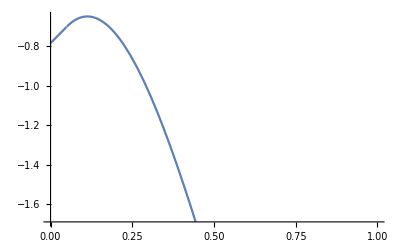

```mathematica
Plot[θBall[t],{t,0,1}]
```